Depth-to-Clusters Mapping

This document defines a fomula to map depth to clusters (or froxels).
This mapping step is necessary to implement Clustered Forward Rendering.

It is important to note that the conversion relies on using a linear depth value.
This value can be either computed from the depth buffer (see the linearZ function),
or come directly from an eye space position in the case of forward rendering.

## Parameters and definitions

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Near plane *)
n=0.1;
(* Far plane *)
f=100.0;
(* Max cluster index *)
maxIndex=16;

(* OpenGL Z linearization, see http://www.humus.name/temp/Linearize%20depth.txt *)
(* This equation assumes Z comes from gl_FragCoord.z *)
(* If Z comes from a depth texture, c0 and c1 are different: *)
(* c0=(1-f/n)/2 *)
(* c1=(1+f/n)/2 *)
c1 = f/n;
c0 = 1.0 - c1;

(* Computes linear z from depth buffer *)
(* This can be optimized to -Log2[] under Log2[] *)
linearZ[z_]:=1.0/(c0*z+c1)

(* Z must be linear *)
zToCluster[z_]:=Log2[z]*(maxIndex/-Log2[n/f])+maxIndex
```

## Depth to cluster index The graphics below shows the assignment of a cluster index to each depth value in the [near, far] range.

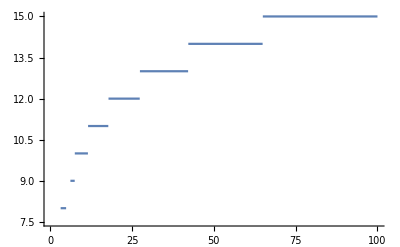

```mathematica
(* This assumes Z is the depth position in eye space, use linearZ[] if Z comes from gl_FragCoord.z *)
Plot[Floor[Max[zToCluster[z/f],0]], {z,n,f},ImageSize->Full]
```

Range loss

Because the distribution is exponential, a large number of clusters is assigned to the first few meters of the depth range.
By plotting the assignments in the range [near, 7m], we can see that almost half of our clusters are already assigned.
This problem is similar to the one observed by Avalanche Studios in Practical Cluster Shading.

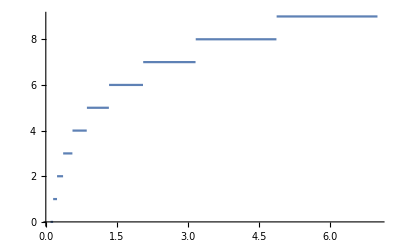

```mathematica
Plot[Floor[Max[zToCluster[z/f],0]], {z,n,7},ImageSize->Full]
```

Fixing the range loss

The solution proposed by Avalanche Studios is to create a special cluster at the near plane and to redistribute
the clusters over the remaining depth range. The far bound of this special cluster depends on the types of scenes
that will be lit using the Clustered Forward Rendering technique.

In the example below, we used the special cluster [near, 5m]. To implement the special cluster, we simply need to
replace the near plane in the original formula with a new near value (in this case, 5). We also need to reduce the
clusters indices range by 0 (maxIndex - 1).

We can observe that the new range presents a better distribution.

5

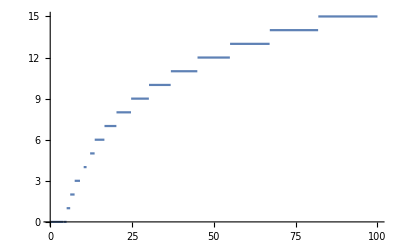

```mathematica
specialNear= 5
zToClusterSpecial[z_]:=Log2[z]*((maxIndex-1)/-Log2[specialNear/f])+maxIndex
Plot[Floor[Max[zToClusterSpecial[z/f],0]], {z,n,f},ImageSize->Full]
```

Cluster index to depth

It is simply the inverse function:

```mathematica
clusterToZ[c_]:=2^((c - maxIndex) / ((maxIndex-1)/-Log2[specialNear/f]))
```